# Bootstrapping O(N) vector model

## Implementation of Appendix A.

This uses the algorithm mentioned in the appendix  to determine a(i).

```mathematica
ClearAll["Global`*"]

UnitarityBound[D_,l_]:=If[l==0,(D-2)/2, l+D-2];

(*Approx[polelist_,y_,Dim_,l_]:=Module[{},
n=Length[polelist];

lhs=1/(x-y);
rhs=Table[1/(x-polelist[[i]]),{i,1,n}];
d=D[#,x]&;

Mat ={};
Col={};
For[k=1,k≤n/2,k++,If[k==1,
AppendTo[Mat,rhs];
AppendTo[Col,lhs];,
AppendTo[Mat,d@Last[Mat]];
AppendTo[Col,d@Last[Col]];
]
];
M={};
b={};
u=UnitarityBound[Dim,l];
M=Join[M,Mat/.{x->u}];
M=Join[M,Mat/.{x->Infinity}];
b=Join[b,Col/.{x->u}];
b=Join[b,Col/.{x->Infinity}];



a=LinearSolve[M,b];
Return [a];]

Approx[{1,2,3,7},7.3,3,3]*)
```

## Implementation of derivatives.

```mathematica
r1=FullSimplify[Together[(Sqrt[z zb]/((1+Sqrt[1-z])*(1+Sqrt[1-zb])))/.{z->(a+Sqrt[b])/N[2,10],zb->(a-Sqrt[b])/N[2,10]}]]
η1= FullSimplify[(((z/(1+Sqrt[1-z])^2)+(zb/(1+Sqrt[1-zb])^2))/(2 r1))/.{z->(a+Sqrt[b])/N[2,10],zb->(a-Sqrt[b])/N[2,10]}]

N20=N[#,10]&;
u=Simplify[(z zb )/.{z->(a+Sqrt[b])/N20@2,zb-> (a-Sqrt[b])/N20@2}];
v=Simplify[((1-z)(1-zb))/.{z->(a+Sqrt[b])/N20@2,zb-> (a-Sqrt[b])/N20@2}];
hlinf[r_,η_,l_,ν_]:=Factorial[l] GegenbauerC[l,ν,η]/( Pochhammer[2ν ,l]*((1-r^2)^ν )*Sqrt[(1+r^2)^2 -4r^2 η^2]);
```

(0.5 √(a^2-b))/((1.+√(1-0.5 (a+√b))) (1.+√(1-0.5 a+0.5 √b)))

1/(√(a^2-b))1. (1.+√(1-0.5 (a+√b))) (1.+√(1-0.5 a+0.5 √b)) ((0.5 (a-√b))/(1+√(1-0.5 a+0.5 √b))^2+(0.5 (a+√b))/(1+√(1-0.5 (a+√b)))^2)

```mathematica
c1[k_,l_,ν_]:=- (k (Factorial[2k])^2 Pochhammer[l+2ν,2k])/(2^(4k-1) Factorial[k]^4 Pochhammer[l+ν,2k]);
c2[k_,l_,ν_]:=- (k(ν+l-k)Pochhammer[ν,k]Pochhammer[1-ν,k] Pochhammer[(ν+l+1-k)/2,k]^2)/(Factorial[k]^2  (l+ν+k) Pochhammer[(ν+l-k)/2,k]^2);
c3[k_,l_,ν_]:=- (k (Factorial[2k])^2 Pochhammer[1+l-2k,2k])/(2^(4k-1) Factorial[k]^4 Pochhammer[l+ν+1-2k,2k])
```

```mathematica
h[Δ_,l_,r_,η_,ν_,depth_]:=Module[{retval,num},

retval=0;

If[depth<5,
num=4-depth;
retval+=Sum[(c1[i,l,ν]* r^(2i)/(Δ-(1-l-2i)))*h[1-l,l+2i,r,η,ν,depth+1] ,{i,1,num,1}];

retval+=Sum[(c2[i,l,ν]* r^(2i)/(Δ-(1+ν-i)))*h[1+ν+i,l,r,η,ν,depth+1] ,{i,1,num,1}];


retval+=Sum[(c3[i,l,ν] *r^(2i)/(Δ-(1+l+2 ν-2i)))*If[l-2i<0,0,h[1+l+2 ν,l-2i,r,η,ν,depth+1]],{i,1,num,1}];

,


retval+=0;

];



Return[
retval+hlinf[r,η,l,ν]];
];

f[a_,b_,β_,l2_]:=((4r)^Δ  h[Δ,N[l2,10],r,η,N[10^-2,10],0])/.{r->r1,η->η1}
```

```mathematica
func[Δp_,lp_,Δ2_,l2_]:=(v^Δp (f[a,b,Δp,l2]/.{Δ->Δ2}) - u^Δp (f[2-a,b,Δp,l2]/.{Δ->Δ2}))/(u^Δp - v ^Δp)
```

```mathematica
(*func[α,0,β,0]*)
```

```mathematica
f[a,b,0,2]/.{a->1,b->0}
```

0.686291501^Δ (1.030638-0.014832205/(-1.02+Δ)-0.00039199864/(-0.01+Δ)-0.0005018178/(0.99+Δ)+(3.686329×10^-11)/(1.99+Δ)+0.00002245906/(2.99+Δ)-0.01533956/(3.+Δ)-0.000509483/(5.+Δ)-0.00001567/(7.+Δ)-(4.7198×10^-7)/(9.+Δ))

```mathematica
D[f[a,0,0,2],{a,1}]/.{a->1,b->0}
```

0.686291501^Δ (0.0892989-0.042912887/(-1.02+Δ)-0.0011223035/(-0.01+Δ)-0.002867618/(0.99+Δ)+(3.152213×10^-10)/(1.99+Δ)+0.0002556714/(2.99+Δ)-0.04501609/(3.+Δ)-0.00292969/(5.+Δ)-0.00013441/(7.+Δ)-(5.384×10^-6)/(9.+Δ))+0.485281374 0.343145751^(-1+Δ) 2.^Δ Δ (1.030638-0.014832205/(-1.02+Δ)-0.00039199864/(-0.01+Δ)-0.0005018178/(0.99+Δ)+(3.686329×10^-11)/(1.99+Δ)+0.00002245906/(2.99+Δ)-0.01533956/(3.+Δ)-0.000509483/(5.+Δ)-0.00001567/(7.+Δ)-(4.7198×10^-7)/(9.+Δ))

```mathematica
k[β_,x_]:=x^(β/N[2,20])*Hypergeometric2F1[β/N[2,20],β/N[2,20],β,x];

G[Δ_,l_,z_,zb_]:=N[0.5,20](k[Δ+l,z]k[Δ-l,zb]+k[Δ+l,zb]k[Δ-l,z]);
```

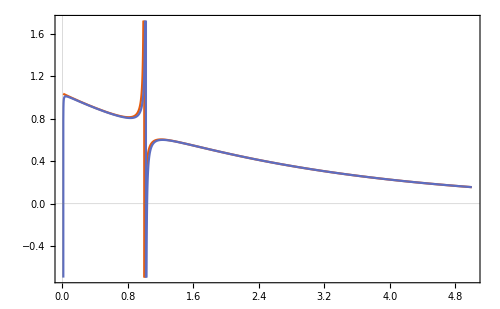

```mathematica
Plot[{G[Δ,2,0.5,0.5],(0.6862915010152396096`9.587407346737212)^Δ (1.0306379865070573391`8.668812687809833-(0.01483220479677925874043114779`8.626983698070482)/(-1.02`9.70324880231529+Δ)-(0.00039199864133107262376054075`8.420521821341065)/(-0.01`10.+Δ)-(0.00050181781562035213354583896`7.190576473387375)/(0.99`11.995635194597547+Δ)+(3.686329398905045691`7.341288863937806*^-11)/(1.99`12.298853076409703+Δ)+(0.00002245905569071273274456391`7.334888296837327)/(2.99`12.475671188324428+Δ)-(0.0153395605294453115`7.649492198817736)/(3.`10.176091259055681+Δ)-(0.00050948256383973186257303234`6.745360760633977)/(5.`10.397940008672037+Δ)-(0.00001566952616181990552058411`5.868722034084741)/(7.`10.544068044350277+Δ)-(4.7197912059395140148929`5.01330720990115*^-7)/(9.`10.653212513775346+Δ))},{Δ,0.01,5},PlotTheme->"Scientific",ImageSize->500]
```

```mathematica
(*((4r)^Δ(hlinf[r,η,0,ν]+r^2(hlinf[r,η,2,ν]*(c1[1,0,ν]/(Δ+1))+hlinf[r,η,0,ν]*(c2[1,0,ν]/(Δ-ν)))))/.{η->1,r-> N[3-2Sqrt[2],10],ν->N[10^-5,20],Δ->3}*)
```

```mathematica
(*TeXForm[0.6862915010152396096^Δ (0.0892989088512541871-0.0429128871100155394/(-1.02+Δ)-0.00112230347984222158189241833/(-0.01+Δ)-0.0028676182565163636/(0.99+Δ)+3.1522125743717146153^-10/(1.99+Δ)+0.0002556713592728518177251275/(2.99+Δ)-0.0450160851282308035/(3+Δ)-0.0029296936400758071/(5+Δ)-0.0001344123382524964/(7+Δ)-5.38350858577164619438343^-6/(9+Δ))]*)

TexForm[(  (1.0306379865070573391-0.01483220479677925874043114779/(-1.02+Δ)-0.00039199864133107262376054075/(-0.01+Δ)-0.00050181781562035213354583896/(0.99+Δ)+3.686329398905045691^-11/(1.99+Δ)+0.00002245905569071273274456391/(2.99+Δ)-0.0153395605294453115/(3+Δ)-0.00050948256383973186257303234/(5+Δ)-0.00001566952616181990552058411/(7+Δ)-4.7197912059395140148929^-7/(9+Δ)))]
```

TexForm[0.3431457505076198047932451032^(-1+Δ) 2^Δ Δ (1.030637986507057339-0.0148322047967792587404311478/(-1.02+Δ)-0.0003919986413310726237605408/(-0.01+Δ)-0.000501817815620352133545839/(0.99+Δ)+(5.8541583021021568×10^-7)/(1.99+Δ)+0.0000224590556907127327445639/(2.99+Δ)-0.015339560529445312/(3+Δ)-0.0005094825638397318625730323/(5+Δ)-0.0000156695261618199055205841/(7+Δ)-0.0000191663975820541153916/(9+Δ))]

```mathematica
TexForm[0.34314575050761980479324510316^(-1+Δ) 2^Δ Δ]
```

```mathematica
TexForm[x]
```

TexForm[x]

```mathematica
deriv[m_,n_,term_]:=D[D[term,{a,2m}],{b,n}];
```